# MOT expansion

## Without gravity

x,y in camera plane of view, z through the cloud.

```mathematica
Clear[fr,wx,wz,wy]
fr0[x_,y_,z_,t_] = Exp[-2 (x^2/wx^2 +z^2/wz^2+((y+1/2 g t^2)^2)/wy^2)]; (* t=0 density, not normalized! *)
```

integrate through the depth of the cloud along the camera’s optical axis

```mathematica
norm = Integrate[fr0[0,0,z,0],{z,-∞,∞}];(*max fl. t=0*)
Integrate[fr0[x,y,z,t],{z,-wz,wz}]/norm(*fluorescence at t=0, eq 13.30*)
```

ConditionalExpression[0.9545 ⅇ^(-(2. x^2)/wx^2+(-48.02 t^4-19.6 t^2 y-2. y^2)/wy^2) √(1/wz^2) wz,Re[wz^2]>0]

```mathematica
wx0 = wy0 = 10^-3; (*[m]*)
kB = 1.3807*10^-23; (*[J/K]*)
g = 9.8; (*[m/s]*)
n = 10^6 ;(* ~ million atoms in MOT? can get number from density and width. see Mark's notes*)
m = n*1.419226*10^-25; (*mass of the cloud of Rb, [kg]*)
T = 100*10^-6; (*[K]*)
wx[t_]:= wx0 Sqrt[1+ 4 kB T t^2/(m wx0^2)];
wy[t_]:= wy0 Sqrt[1+ 4 kB T t^2/(m wy0^2)];
```

```mathematica
F[t_,x_,y_] := (2/(π wx[t] wy[t]))^(3/2)*(2/(π wx[0] wy[0]))^(-3/2)Exp[-(2 x^2)/wx[t]^2-(2 y^2)/wy[t]^2]; (*normalized to peak fluorescence at t=0*)
```

Slice of x = 0 in xy plane of mot fluorescence for various times [s]

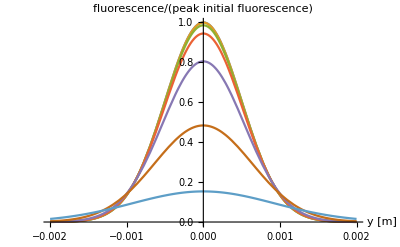

```mathematica
Plot[Evaluate[Table[F[t,0,y],{t,{0,.1,.5,1,2,4,8}}]],{y,-2*wy[0],2*wy[0]},AxesLabel->{"y [m]","fluorescence/(peak initial fluorescence)"}]
```

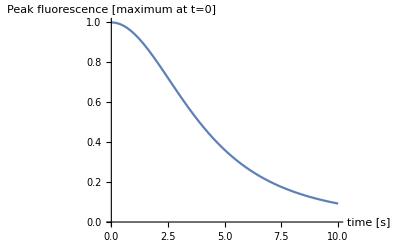

```mathematica
Plot[F[t,0,0],{t,0,10}, AxesLabel->{"time [s]","Peak fluorescence [maximum at t=0]"}]
```

## With gravity

```mathematica
wx0 = wy0 = 10^-3; (*[m]*)
kB = 1.3807*10^-23; (*[J/K]*)
g = 9.8; (*[m/s]*)
m = 1.419226*10^-25; (*mass of Rb, [kg]*)
Clear[T]
wx[t_,T_]:= wx0 Sqrt[1+ 4 kB T t^2/(m wx0^2)];
wy[t_,T_]:= wy0 Sqrt[1+ 4 kB T t^2/(m wy0^2)];
```

```mathematica
Fg[t_,x_,y_,T_] := (2/(π wx[t,T] wy[t,T]))^(3/2)*(2/(π wx[0,T] wy[0,T]))^(-3/2)Exp[-(2 x^2)/wx[t,T]^2-(2 (y+1/2 g t^2)^2)/wy[t,T]^2]; (*normalized to peak fluorescence at t=0*)
```

```mathematica
Tlist = {200*10^-6,150*10^-6,100*10^-6,50*10^-6,25*10^-6};
```

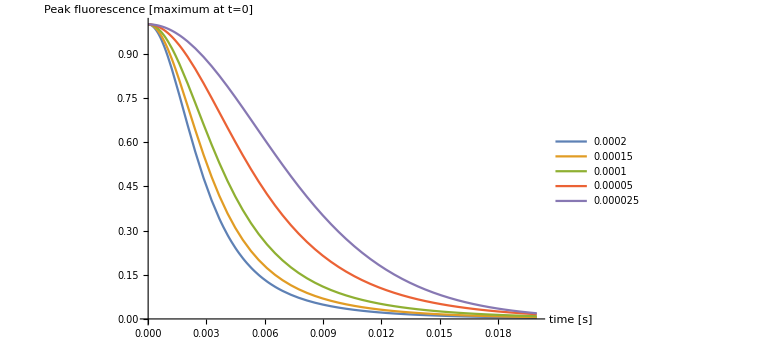

```mathematica
Plot[Evaluate[Table[Fg[t,0,0,T],{T,Tlist}]],{t,0,.02}, AxesLabel->{"time [s]","Peak fluorescence [maximum at t=0]"},
PlotLegends->N[Tlist],ImageSize->Large]
```